# BSM Seminar — KIT

## December 5, 2022

## HighPT — Constraining NP with high-p_T Drell-Yan tails

## Installation

To use the automatic installation simply uncomment and evaluate the following cell

```mathematica
(*Import["https://github.com/HighPT/HighPT/raw/master/install.m"]*)
```

## Loading HighPT

Uncomment the code below if you have installed HighPT outside Mathematica’s base directory. Not required after automatic installation.

```mathematica
(*PrependTo[$Path,"path/to/HighPT/installation"];*)
```

The HighPT package can be loaded by evaluating “<<HighPT`”.

```mathematica
<<HighPT`
```

By default the SMEFT mode is activated, only d=6 operators are considered, the EFT series is truncated at Λ^-4, and the EFt scale is set to Λ=1 TeV.

## Overview & help for all functions

Blow you can find a list of all HighPT routines. You can click on any of them to get detailed information about it.

```mathematica
?HighPT`*
```

## Initializing the SMEFT mode

Launch the SMEFT mode working:
- up to 𝒪(Λ^-4),
- with d=6 operators,
- setting Λ=2 TeV.

```mathematica
InitializeModel["SMEFT",
EFTorder->4,
OperatorDimension->6,
EFTscale->2000
]
```

## Reproduce the constraints for the U_1 leptoquark model

Consider the U_1 Lagrangian:  ℒ_U_1=[x_1^L]^iα((q̄)_i γ_μ U_1^μ l_α)+h.c.
The tree-level matching condition to the SMEFT Warsaw basis are: [C_lq^(1)]_αβij=[C_lq^(3)]_αβij=-(((1/2[x_1^L])_iβ[x_1^L])_jα)^*
Re-derive the high-p_T constraints for this model for couplings to 3rd generation leptons, and 3rd & 2nd generation quarks. Furthermore set the mass of the leptoquark to 2 TeV.

-Graphics-

#### Likelihood

Access the documentation of the χ^2 function (works similar for all other functions).

```mathematica
?ChiSquareLHC
```

Deriving the χ^2 likelihood for pp→ττ, keeping only the required Wilson coefficients.

```mathematica
χττSMEFTbinned=ChiSquareLHC["di-tau-ATLAS",
Coefficients->{
WC["lq1",{3,3,3,3}],(* flavor indices {l,l,q,q} *)
WC["lq1",{3,3,2,3}],
WC["lq1",{3,3,2,2}],
WC["lq3",{3,3,3,3}],
WC["lq3",{3,3,2,3}],
WC["lq3",{3,3,2,2}]
}
];
```

The result is a list containing the likelihood for all the experimental bin. (In this case we have 14 bins.)

```mathematica
χττSMEFTbinned//Length
```

The total χ^2 is obtained summing all the bins

```mathematica
χττSMEFT=Total[χττSMEFTbinned]//Expand;
```

Deriving the χ^2 likelihood for pp→τν [this is a bit more time consuming]

```mathematica
(*
χτνSMEFTbinned=ChiSquareLHC["mono-tau-ATLAS",
Coefficients->{WC["lq1",{3,3,3,3}],WC["lq1",{3,3,2,3}],WC["lq3",{3,3,3,3}],WC["lq3",{3,3,2,3}]}
];
χττSMEFT=χττSMEFT+Total[χτνSMEFTbinned];
*)
```

Match the SMEFT Wilson coefficients to the U_1 couplings

```mathematica
χττSMEFTU1=χττSMEFT/.{
WC["lq1",{3,3,i_,j_}]:>-1/2 Coupling["x1L",{i,3}]Coupling["x1L",{j,3}]*,
WC["lq3",{3,3,i_,j_}]:>-1/2 Coupling["x1L",{i,3}]Coupling["x1L",{j,3}]*
};
```

Assume that all couplings are real

```mathematica
Coupling/:Conjugate[Coupling[a___]]:=Coupling[a];
```

Printing the likelihood

```mathematica
χττSMEFTU1
```

Printing using TraditionalForm

```mathematica
χττSMEFTU1//TraditionalForm
```

The likelihood can contain small imaginary parts as numerical artifacts.

Remove small imaginary parts:

```mathematica
χττSMEFTU1=Chop[χττSMEFTU1];
%//TraditionalForm
```

#### Minimizing the likelihood

Numerical minimization of the likelihood w.r.t. the two couplings of interest.

```mathematica
{min,bestfit}=NMinimize[χττSMEFTU1,{Coupling["x1L",{2,3}],Coupling["x1L",{3,3}]},Method->"RandomSearch"]
```

#### Plotting the results

Plotting the 95% CL region (Δχ^2=5.99 for a two parameter fit)

```mathematica
RegionPlot[
χττSMEFTU1<=5.99+min,
{Coupling["x1L",{2,3}],-1.5,+1.5},
{Coupling["x1L",{3,3}],-3.7,+3.7}
,
FrameLabel->{"[x_1^L]_23","[x_1^L]_33"}
]
```

### U_1 model

Initialize the BSM mediator mode with a 2 TeV U_1 leptoquark with zero width.

```mathematica
InitializeModel["Mediators",
Mediators->{"U1"->{2000,0}}(* add Subscript[U, 1] leptoquark with mass 2 TeV and zero width *)
]
```

The U_1 is a t-channel mediator that contributes to vector and scalar currents in the Warsaw basis.

#### Likelihood

Derive the total likelihood for pp→ττ, considering only the relevant couplings.

```mathematica
χττU1=(ChiSquareLHC["di-tau-ATLAS",
Coefficients->{Coupling["x1L",{2,3}],Coupling["x1L",{3,3}]}
]//Total//Expand)/.Complex[a_,b_]:>a;
χττU1//TraditionalForm
```

#### Minimization

Minimize the likelihood w.r.t. the two relevant couplings.

```mathematica
{minU1,bestfitU1}=NMinimize[χττU1,{Coupling["x1L",{2,3}],Coupling["x1L",{3,3}]},Method->"RandomSearch"]
```

#### Plotting

Plot the 95% CL region.

```mathematica
RegionPlot[
χττU1<=5.99+minU1,
{Coupling["x1L",{2,3}],-1.5,+1.5},
{Coupling["x1L",{3,3}],-3.7,+3.7}
,
FrameLabel->{"[x_1^L]_23","[x_1^L]_33"}
]
```

### Comparison EFT vs full model

Comparison of the bounds obtained in the SMEFT mode and using the BSM model with the full U_1 propagator information.

```mathematica
RegionPlot[
{χττSMEFTU1<=5.99+min,χττU1<=5.99+minU1},
{Coupling["x1L",{2,3}],-1.5,+1.5},
{Coupling["x1L",{3,3}],-3.7,+3.7}
,
PlotLegends->{"EFT","U_1 model"},
FrameLabel->{"[x_1^L]_23","[x_1^L]_33"}
]
```

We find good agreement of the constraints, showing that for a 2 TeV leptoquark, the EFT approach is valid.

## Exercise

Repeat the above analysis for the R_2 leptoquark model (with mass m_R_2=2 TeV) with Lagrangian: 
ℒ_R_2=-[y_2^L]_iα((ū)_i R_2 ϵ l_α)+[y_2^R]_iα((q̄)_i e_α R_2)+h.c.

Hint: the tree-level matching to the SMEFT gives:
[C_lequ^(1)]_αβij=(4[C_lequ^(3)])_αβij=-(((1/2[y_2^R])_iβ[y_2^L])_jα)^*
[C_lu]_αβij=-(((1/2[y_2^L])_iβ[y_2^L])_jα)^*
[C_eq]_αβij=-(((1/2[y_2^R])_iβ[y_2^R])_jα)^*
(notice that we define [C_eq]_αβij=[C_qe]_ijαβ)

Assume only [y_2^R]_33 and [y_2^L]_23 are non-vanishing and real!

Repeat the steps above for m_R_2=1 TeV.

## Solution

### 2 TeV

#### SMEFT

```mathematica
(* Initialize SMEFT *)
InitializeModel["SMEFT",
EFTorder->4,
OperatorDimension->6,
EFTscale->2000
]

(* list the relevant Wilson coefficients and their matching conditions *)
R2wcList={
WC["lequ1",{3,3,3,2}],
WC["lequ3",{3,3,3,2}],
WC["lu",{3,3,2,2}],
WC["eq",{3,3,3,3}]
};
R2wcReplacements={
WC["lequ1",{3,3,i_,j_}]:>-1/2 Coupling["y2R",{i,3}]Coupling["y2L",{j,3}]*,
WC["lequ3",{3,3,i_,j_}]:>-1/8 Coupling["y2R",{i,3}]Coupling["y2L",{j,3}]*,
WC["lu",{3,3,i_,j_}]:>-1/2 Coupling["y2L",{i,3}]Coupling["y2L",{j,3}]*,
WC["eq",{3,3,i_,j_}]:>-1/2 Coupling["y2R",{i,3}]Coupling["y2R",{j,3}]*
};

(* compute SMEFT likelihood *)
χR2SMEFT=(ChiSquareLHC["di-tau-ATLAS",Coefficients->R2wcList]//Total//Expand)/.R2wcReplacements/.Complex[a_,b_]:>a;

(* minimize SMEFT likelihood *)
{minR2SMEFT,bestfitR2SMEFT}=NMinimize[χR2SMEFT,{Coupling["y2L",{2,3}],Coupling["y2R",{3,3}]}]
```

#### R_2 model

```mathematica
(* Initialize R2 model *)
InitializeModel["Mediators",
Mediators->{"R2"->{2000,0}}
]
 
(* compute R2 likelihood *)
χR2=(ChiSquareLHC["di-tau-ATLAS",Coefficients->{Coupling["y2R",{3,3}],Coupling["y2L",{2,3}]}]//Total//Expand)/.Complex[a_,b_]:>a;

(* minimize SMEFT likelihood *)
{minR2,bestfitR2}=NMinimize[χR2,{Coupling["y2L",{2,3}],Coupling["y2R",{3,3}]}]
```

#### Comparison

Compare the SMEFT bounds with the bounds from the full leptoquark model.

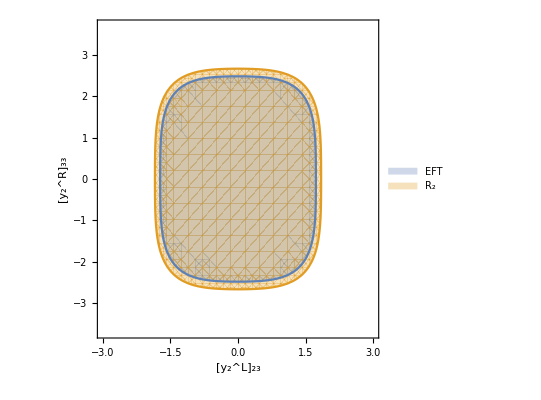

```mathematica
RegionPlot[
{χR2SMEFT<=5.99+minR2SMEFT,χR2<=5.99+minR2},
{Coupling["y2L",{2,3}],-3,+3},
{Coupling["y2R",{3,3}],-3.7,+3.7}
,
PlotLegends->{"EFT","R_2"},
FrameLabel->{"[y_2^L]_23","[y_2^R]_33"}
]
```

Again we find good agreement between the constraints, validating the EFT approach for a 2 TeV leptoquark.

### 1 TeV

#### SMEFT

```mathematica
(* Initialize SMEFT *)
InitializeModel["SMEFT",
EFTorder->4,
OperatorDimension->6,
EFTscale->1000
]

(* list the relevant Wilson coefficients and their matching conditions *)
R2wcList={
WC["lequ1",{3,3,3,2}],
WC["lequ3",{3,3,3,2}],
WC["lu",{3,3,2,2}],
WC["eq",{3,3,3,3}]
};
R2wcReplacements={
WC["lequ1",{3,3,i_,j_}]:>-1/2 Coupling["y2R",{i,3}]Coupling["y2L",{j,3}]*,
WC["lequ3",{3,3,i_,j_}]:>-1/8 Coupling["y2R",{i,3}]Coupling["y2L",{j,3}]*,
WC["lu",{3,3,i_,j_}]:>-1/2 Coupling["y2L",{i,3}]Coupling["y2L",{j,3}]*,
WC["eq",{3,3,i_,j_}]:>-1/2 Coupling["y2R",{i,3}]Coupling["y2R",{j,3}]*
};

(* compute SMEFT likelihood *)
χR2SMEFT=(ChiSquareLHC["di-tau-ATLAS",Coefficients->R2wcList]//Total//Expand)/.R2wcReplacements/.Complex[a_,b_]:>a;

(* minimize SMEFT likelihood *)
{minR2SMEFT,bestfitR2SMEFT}=NMinimize[χR2SMEFT,{Coupling["y2L",{2,3}],Coupling["y2R",{3,3}]}]
```

#### R_2 model

```mathematica
(* Initialize R2 model *)
InitializeModel["Mediators",
Mediators->{"R2"->{1000,0}}
]
 
(* compute R2 likelihood *)
χR2=(ChiSquareLHC["di-tau-ATLAS",Coefficients->{Coupling["y2R",{3,3}],Coupling["y2L",{2,3}]}]//Total//Expand)/.Complex[a_,b_]:>a;

(* minimize SMEFT likelihood *)
{minR2,bestfitR2}=NMinimize[χR2,{Coupling["y2L",{2,3}],Coupling["y2R",{3,3}]}]
```

#### Comparison

Compare the SMEFT bounds with the bounds from the full leptoquark model.

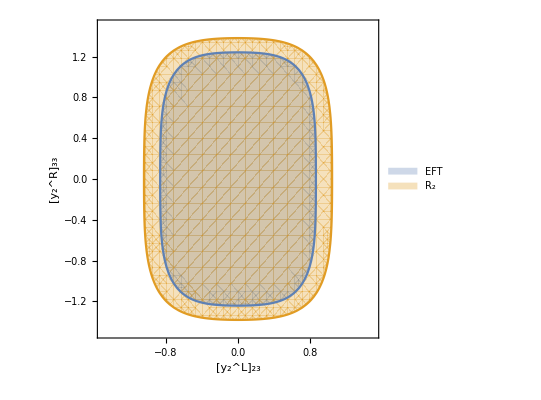

```mathematica
RegionPlot[
{χR2SMEFT<=5.99+minR2SMEFT,χR2<=5.99+minR2},
{Coupling["y2L",{2,3}],-1.5,+1.5},
{Coupling["y2R",{3,3}],-1.5,+1.5}
,
PlotLegends->{"EFT","R_2"},
FrameLabel->{"[y_2^L]_23","[y_2^R]_33"}
]
```

We see that the agreement of the EFT validity is starting to break down.